## Mathematical model of bone expansion during skull morphogenesis

Supplement to the paper:
Self-propagating wave drives morphogenesis of skull bones in vivo
Yiteng Dang, Johanna Lattner, Adrian A. Lahola-Chomiak, Diana Alves Afonso, Elke Ulbricht, Anna Taubenberger, Steffen Rulands, Jacqueline M. Tabler

In this script, we simulate the mathematical model described in the paper above (details in Supplementary Text), examine the results of the simulation and export the simulated data for further processing in other scripts. We start by defining the model in equation form, then explicitly discretize the model using a finite differences scheme and solve the discretized model. The results are plotted using kymographs and time snapshots, compared to experimental results and saved in CSV format. For generating higher-quality plots for publication, we use other scripts in Python and R.

```mathematica
Clear["Global`*"]
```

## Set up model

First, we set up the mathematical model by defining all model and system parameters, initial and boundary condition and the full PDE system in equation form.

### Parameters

Model parameters
ρdA, ρdB: Carrying capacities of A and B cells
D: Diffusion constant
eO, eM: Stiffnesses of cell types A and B
τ: Relaxation timescale of the growth rate
η: Viscosity
γ: Friction
α: Proportionality constant in definition of differentiation rate k_D
ρh: Homeostatic density, at which the pressure is zero
aρ, aϕ: Steepness of the initial profile for ρ and ϕ respectively

System size parameter
L: domain size in microns
tmax: simulation time in hours
Nx: number of steps in the space discretization
T:  number of steps in the time discretization

Recommendations
* It is required that ρ_h > ρ_A, ρ_B in order to get reasonable results for the velocity, so we get the pressure P>0 everywhere. 
* Tune γ to tune the overall speed of individual cells.
* Tune α to tune the expansion speed without affecting V.
* The solvers work well only for an (unknown) region of the parameter space. Also, changing system size and discretization parameters (L, tmax, Nx, T) may cause numerical issues.

```mathematica
(* Convert units to hours and μm *)
PaToNewUnits=1/(10^(6)*(1/3600)^2); 
SecToHr = 1/3600;
(* Define all parameters *) 
params={ρdA->0.0067,ρdB->0.0077,D1->15,eO->1000*PaToNewUnits,eM->30*PaToNewUnits,τ->10,η->10^3*PaToNewUnits*SecToHr,γ->0.8*10^3*PaToNewUnits*SecToHr,α->3.5*10^(-6),ρh->1/1000,aρ->4,aϕ->4}; 
(* Simulation settings*)
L=1500;
tmax=8;
Nx=200;
T=100;
```

#### Initial and boundary conditions

Define the profiles of ρ(x) and ϕ(x) at the initial time. The solution for v(x) is computed by solving an ODE depending on ρ(x) and ϕ(x) later on and is set to 0 initially.

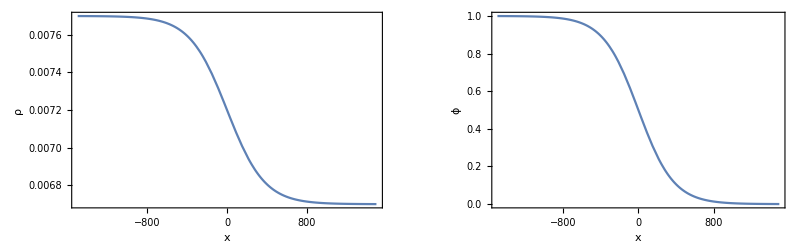

```mathematica
ρ0[x_]:=(Tanh[aρ x/L]+1)/2 (ρdA-ρdB)+ ρdB;
ϕ0[x_]:=(1-Tanh[aϕ x/L])/2;
iv={ρ[x,0]==ρ0[x],ϕ[x,0]==ϕ0[x],v[x,0]==0} /. params;
bc={ρ[-L,t]==ρ0[-L],ρ[L,t]==ρ0[L],ϕ[-L,t]==ϕ0[-L],ϕ[L,t]==ϕ0[L],v[-L,t]==0,v[L,t]==0} /. params;

GraphicsRow[{Plot[{ρ0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "ρ"}], Plot[{ϕ0[x]} /. params, {x, -L, L}, Frame-> True, FrameLabel->{"x", "ϕ"}]}]
```

#### PDE system

Define the full PDE system to be solved in terms of a set of equations along with boundary conditions and initial conditions.

```mathematica
(* Compound variables *)
(* Net growth rates *)
kA:=1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB); 
(* Stiffness *)
e:= (eM(1-ϕ[x,t])+eO ϕ[x,t]);
(* Differentiation rate *)
kD:=α (e-eM);

(* Full PDE system *)
PDEsys={D[ρ[x,t],t]+D[ρ[x,t] (v[x,t]),x]==(kA (1-ϕ[x,t])+kB ϕ[x,t]) ρ[x,t],D[ϕ[x,t],t]+(v[x,t]) D[ϕ[x,t],x]==D1 D[ϕ[x,t],{x,2}]+ D1 D[ρ[x,t],x] D[ϕ[x,t],x]/ρ[x,t]+(kB-kA) ϕ[x,t] (1-ϕ[x,t])+kD (1-ϕ[x,t]),
ρ[x,t](η D[v[x,t],{x,2}]-γ v[x,t])==e D[ρ[x,t],x] + D[e, x] Log[ρ[x,t]/ρh]*ρ[x,t] };
vars={ρ,ϕ,v};
fullsys=Join[PDEsys/.params,bc,iv]
```

{ρ^(0,1)[x,t]+ρ[x,t] v^(1,0)[x,t]+v[x,t] ρ^(1,0)[x,t]==ρ[x,t] (14.9254 (0.0067-ρ[x,t]) (1-ϕ[x,t])+12.987 (0.0077-ρ[x,t]) ϕ[x,t]),ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==(-14.9254 (0.0067-ρ[x,t])+12.987 (0.0077-ρ[x,t])) (1-ϕ[x,t]) ϕ[x,t]+3.5×10^-6 (1-ϕ[x,t]) (-1944/5+1944/5 (1-ϕ[x,t])+12960 ϕ[x,t])+(15 ρ^(1,0)[x,t] ϕ^(1,0)[x,t])/ρ[x,t]+15 ϕ^(2,0)[x,t],ρ[x,t] (-2.88 v[x,t]+18/5 v^(2,0)[x,t])==(1944/5 (1-ϕ[x,t])+12960 ϕ[x,t]) ρ^(1,0)[x,t]+62856/5 Log[1000 ρ[x,t]] ρ[x,t] ϕ^(1,0)[x,t],ρ[-1500,t]==0.00769966,ρ[1500,t]==0.00670034,ϕ[-1500,t]==1/2 (1+Tanh[4]),ϕ[1500,t]==1/2 (1-Tanh[4]),v[-1500,t]==0,v[1500,t]==0,ρ[x,0]==0.0077-0.0005 (1+Tanh[x/375]),ϕ[x,0]==1/2 (1-Tanh[x/375]),v[x,0]==0}

## Discretized model and simulate

In this section, we discretize the PDE model defined above using finite difference methods and numerically solve it according to one of the several discretization schemes defined below. Note that we chose this explicit discretization over Mathematica’s built-in NDSolve function because the latter tends to be unstable when solving a complicated system of coupled PDEs.

### Define discretized PDE system

We have implemented several discretization schemes below:
1. Forward Euler scheme
2. Backward Euler scheme
3. Crank-Nicholson scheme
4. Upwind scheme
In practice, we preferred solving using the first scheme (forward Euler) as this appeared to most reliably generate results for a range of parameters.

```mathematica
PDEsys
```

{ρ^(0,1)[x,t]+ρ[x,t] v^(1,0)[x,t]+v[x,t] ρ^(1,0)[x,t]==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),ϕ^(0,1)[x,t]+v[x,t] ϕ^(1,0)[x,t]==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 ρ^(1,0)[x,t] ϕ^(1,0)[x,t])/ρ[x,t]+D1 ϕ^(2,0)[x,t],ρ[x,t] (-γ v[x,t]+η v^(2,0)[x,t])==(eM (1-ϕ[x,t])+eO ϕ[x,t]) ρ^(1,0)[x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM ϕ^(1,0)[x,t]+eO ϕ^(1,0)[x,t])}

```mathematica
(* Equations for PDE *)
(* Time derivative*)
discretizationT={Derivative[0,1][ρ][x,t]->  (Subscript[ρ, i,m+1]-Subscript[ρ, i,m])/Δt, Derivative[0,1][ϕ][x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt}; (* forward scheme*)

(* 1. forward Euler schemes*)
(* a. explicit scheme, centered diff *)
discretization1 = 
{ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx), ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,
v[x,t]-> Subscript[v, i,m], Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx),Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2};
pdeDiscretized1 = PDEsys /.discretizationT /. discretization1;

(* b. explicit scheme, fwd diff *)
(*discretization1b = {ϕ[x,t]-> Subscript[ϕ, i,m], ϕ^(0,1)[x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt,ϕ^(1,0)[x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i,m])/(2 Δx),ϕ^(2,0)[x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,V[x,t]-> Subscript[V, i,m], V^(2,0)[x,t]-> (Subscript[V, i+1,m]- 2 Subscript[V, i,m] + Subscript[V, i-1,m])/(Δx)^2};  
pdeDiscretized =PDEsys /.discretizationT /. discretization1b;*) 

(* 2. backward Euler scheme *) 
(* implicit scheme, centered diff *)
(* NB cannot use implicit scheme for equation for V*)
discretization2 = Join[{ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx),ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2}/.{m->m+1}, {v[x,t]-> Subscript[v, i,m],Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx), Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2}];

pdeDiscretized2 =Join[ PDEsys[[;;2]]/.discretizationT /. discretization2, {PDEsys[[3]]/.discretizationT /. discretization1}];

(* 3. Crank-Nicolson scheme: combine discretizations *)
discretization3= {ρ[x,t]->( Subscript[ρ, i,m] + Subscript[ρ, i,m+1])/2, Derivative[1,0][ρ][x,t]-> ((Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx)+(Subscript[ρ, i+1,m+1]-Subscript[ρ, i-1,m+1])/(2 Δx))/2,ϕ[x,t]-> (Subscript[ϕ, i,m]+Subscript[ϕ, i,m+1])/2, Derivative[1,0][ϕ][x,t]-> ((Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx)+(Subscript[ϕ, i+1,m+1]-Subscript[ϕ, i-1,m+1])/(2 Δx))/2,Derivative[2,0][ϕ][x,t]-> ((Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2+(Subscript[ϕ, i+1,m+1]- 2 Subscript[ϕ, i,m+1] + Subscript[ϕ, i-1,m+1])/(Δx)^2)/2,
v[x,t]-> (Subscript[v, i,m]+Subscript[v, i,m+1])/2,Derivative[1,0][v][x,t]-> ((Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx)+(Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx))/2, Derivative[2,0][v][x,t]->( (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2+(Subscript[v, i+1,m+1]- 2 Subscript[v, i,m+1] + Subscript[v, i-1,m+1])/(Δx)^2)/2};
```

Upwind scheme
The idea of the upwind scheme is to replace derivatives in for the advection terms by upwind terms while keeping the rest the same. This supposedly gives more stability but in practice seems to be very slow to solve.

```mathematica
(*  4. Upwind scheme for 1st derivaties *)
(*upwind1 = {ρ^(1,0)[x,t]-> (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx, v^(1,0)[x,t]-> (Subscript[v, i,m]-Subscript[v, i-1,m])/Δx, ϕ^(1,0)[x,t]-> (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx};*)

PDEsysUpwind=
{Derivative[0,1][ρ][x,t]+ρ[x,t] (Subscript[v, i,m]-Subscript[v, i-1,m])/Δx+v[x,t] (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-γ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 
PDEsysUpwind1b=
{Derivative[0,1][ρ][x,t]+ρ[x,t] Derivative[1,0][v][x,t]+v[x,t] (Subscript[ρ, i,m]-Subscript[ρ, i-1,m])/Δx==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (Subscript[ϕ, i,m]-Subscript[ϕ, i-1,m])/Δx==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-γ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 

(*upwind2 = {ρ^(1,0)[x,t]-> (3 Subscript[ρ, i,m]- 4 Subscript[ρ, i-1,m] + Subscript[ρ, i-2,m])/(2Δx), v^(1,0)[x,t]-> (3 Subscript[v, i,m]-4 Subscript[v, i-1,m]+Subscript[v, i-2,m])/(2 Δx), ϕ^(1,0)[x,t]-> (3 Subscript[ϕ, i,m] - 4 Subscript[ϕ, i-1,m] + Subscript[ϕ, i,m])/(2 Δx)}; (* 2nd order upwind*) *)
PDEsysUpwind2=
{Derivative[0,1][ρ][x,t]+ρ[x,t] (3 Subscript[v, i,m]-4 Subscript[v, i-1,m]+Subscript[v, i-2,m])/(2 Δx)+v[x,t] (3 Subscript[ρ, i,m]- 4 Subscript[ρ, i-1,m] + Subscript[ρ, i-2,m])/(2Δx)==ρ[x,t] (((ρdA-ρ[x,t]) (1-ϕ[x,t]))/(ρdA τ)+((ρdB-ρ[x,t]) ϕ[x,t])/(ρdB τ)),Derivative[0,1][ϕ][x,t]+v[x,t] (3 Subscript[ϕ, i,m] - 4 Subscript[ϕ, i-1,m] + Subscript[ϕ, i,m])/(2 Δx)==(-(ρdA-ρ[x,t])/(ρdA τ)+(ρdB-ρ[x,t])/(ρdB τ)) (1-ϕ[x,t]) ϕ[x,t]+α (1-ϕ[x,t]) (-eM+eM (1-ϕ[x,t])+eO ϕ[x,t])+(D1 Derivative[1,0][ρ][x,t] Derivative[1,0][ϕ][x,t])/ρ[x,t]+D1 Derivative[2,0][ϕ][x,t],ρ[x,t] (-γ v[x,t]+(ηM (1-ϕ[x,t])+ηO ϕ[x,t]) Derivative[2,0][v][x,t])==f+(eM (1-ϕ[x,t])+eO ϕ[x,t]) Derivative[1,0][ρ][x,t]+Log[ρ[x,t]/ρh] ρ[x,t] (-eM Derivative[1,0][ϕ][x,t]+eO Derivative[1,0][ϕ][x,t])}; 

pdeDiscretized4 =PDEsysUpwind /. discretization1 /.discretizationT;
pdeDiscretized4b =PDEsysUpwind1b/. discretization1 /.discretizationT;
pdeDiscretized42 =PDEsysUpwind2 /. discretization1 /.discretizationT;
pdeDiscretized4
```

{((-v_(-1+i,m)+v_(i,m)) ρ_(i,m))/Δx+(v_(i,m) (-ρ_(-1+i,m)+ρ_(i,m)))/Δx+(-ρ_(i,m)+ρ_(i,1+m))/Δt==ρ_(i,m) (((ρdA-ρ_(i,m)) (1-ϕ_(i,m)))/(ρdA τ)+((ρdB-ρ_(i,m)) ϕ_(i,m))/(ρdB τ)),(v_(i,m) (-ϕ_(-1+i,m)+ϕ_(i,m)))/Δx+(-ϕ_(i,m)+ϕ_(i,1+m))/Δt==(-(ρdA-ρ_(i,m))/(ρdA τ)+(ρdB-ρ_(i,m))/(ρdB τ)) (1-ϕ_(i,m)) ϕ_(i,m)+α (1-ϕ_(i,m)) (-eM+eM (1-ϕ_(i,m))+eO ϕ_(i,m))+(D1 (-ρ_(-1+i,m)+ρ_(1+i,m)) (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(4 Δx^2 ρ_(i,m))+(D1 (ϕ_(-1+i,m)-2 ϕ_(i,m)+ϕ_(1+i,m)))/Δx^2,ρ_(i,m) (-γ v_(i,m)+((v_(-1+i,m)-2 v_(i,m)+v_(1+i,m)) (ηM (1-ϕ_(i,m))+ηO ϕ_(i,m)))/Δx^2)==f+((-ρ_(-1+i,m)+ρ_(1+i,m)) (eM (1-ϕ_(i,m))+eO ϕ_(i,m)))/(2 Δx)+Log[(ρ_(i,m))/ρh] ρ_(i,m) (-(eM (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx)+(eO (-ϕ_(-1+i,m)+ϕ_(1+i,m)))/(2 Δx))}

Choose discretization
Below we choose which of the above discretizations to use.

```mathematica
(* Choose discretization out of above options *)
pdeDiscretized = pdeDiscretized1;
Simplify[pdeDiscretized/.params]
```

{((-2 Δx-Δt v_(-1+i,m)+Δt v_(1+i,m)) ρ_(i,m)+2 Δx ρ_(i,1+m)+Δt v_(i,m) (-ρ_(-1+i,m)+ρ_(1+i,m)))/(2 Δt Δx)==1.93836 ρ_(i,m) (0.05159-7.15955×10^-18 ϕ_(i,m)+ρ_(i,m) (-7.7+1. ϕ_(i,m))),-(0.5 (7.5 ρ_(-1+i,m)+(30.+Δx v_(i,m)) ρ_(i,m)-7.5 ρ_(1+i,m)) ϕ_(-1+i,m))/(Δx^2 ρ_(i,m))+(-0.0439992-1./Δt+30./Δx^2) ϕ_(i,m)+0.0439992 ϕ_(i,m)^2+ρ_(i,m) ϕ_(i,m) (-1.93836+1.93836 ϕ_(i,m))+(1. ϕ_(i,1+m))/Δt-(15. ϕ_(1+i,m))/Δx^2+(0.5 v_(i,m) ϕ_(1+i,m))/Δx+((3.75 ρ_(-1+i,m)-3.75 ρ_(1+i,m)) ϕ_(1+i,m))/(Δx^2 ρ_(i,m))==0,(64.8 (-0.0444444 (-1.25 v_(-1+i,m)+(2.5+1. Δx^2) v_(i,m)-1.25 v_(1+i,m)) ρ_(i,m)+Δx (ρ_(-1+i,m) (3+97 ϕ_(i,m))-ρ_(1+i,m) (3+97 ϕ_(i,m))+97 Log[1000 ρ_(i,m)] ρ_(i,m) (ϕ_(-1+i,m)-ϕ_(1+i,m)))))/Δx^2==0}

### Solve discretized system

Next, the system is solved on a grid defined by meshes in x and t. Then the system is solved by looping over time. At a given time t, the profile for V is solved for with the profiles for ρ and ϕ of the same time point t, then the solutions for ρ and ϕ are obtained for the next timestep t+1, followed by solving for V at time t+1, and so on.

First, we define the mesh.

```mathematica
(*Define mesh*)
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
Print[xmesh[[Nx/2+1]]];
Print[ N@ΔxSet]
Print[ N@ΔtSet]
```

0

15.

0.08

CFL condition
This condition for wave solutions is required for convergence. Typically, C=(u Δt)/Δx ≤ C_max with C_max=1.
The velocity u (corresponding to the advection velocity) needs to be estimated.

```mathematica
vmax=20; (*estimation of max velocity*)
N[ ((ρdA+ρdB)/2/.params)  ΔtSet/ΔxSet] (* ρ[x,t] v^(1,0)[x,t]*)
N[ vmax  ΔtSet/ΔxSet] (*v[x,t] ρ^(1,0)[x,t]*) (*v[x,t] ϕ^(1,0)[x,t]*)
```

0.0000384

0.106667

Next, we define the boundary conditions and initial conditions for the discretized system.

```mathematica
(* Boundary conditions *)
ρL=ρ0[-L] /. params; ρR=ρ0[L] /. params; 
(*ϕL = 1; ϕR = 0;*)
ϕL=ϕ0[-L]/.params; ϕR=ϕ0[L]/.params;
VL=0; VR=0;

(* normal *)
bcρ={Subscript[ρ, 0,m]==ρL,Subscript[ρ, Nx,m]==ρR};
bcϕ={Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR};
bcV={Subscript[v, 0,m]==VL,Subscript[v, Nx,m]==VR};
bcρRepl={Subscript[ρ, 0,m]-> ρL,Subscript[ρ, Nx,m]->ρR};
bcϕRepl={Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR};
bcVRepl={Subscript[v, 0,m]-> VL,Subscript[v, Nx,m]->VR};

(* 2nd order upwind *)
bcρ2={Subscript[ρ, -1,m]==ρL,Subscript[ρ, 0,m]==ρL,Subscript[ρ, Nx,m]==ρR,Subscript[ρ, Nx+1,m]==ρR};
bcϕ2={Subscript[ϕ, -1,m]==ϕL,Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR,Subscript[ϕ, Nx+1,m]==ϕR};
bcV2={Subscript[v, -1,m]==VL,Subscript[v, 0,m]==VL,Subscript[v, Nx,m]==VR,Subscript[v, Nx+1,m]==VR};
bcρRepl2={Subscript[ρ, -1,m]-> ρL,Subscript[ρ, 0,m]-> ρL,Subscript[ρ, Nx,m]->ρR,Subscript[ρ, Nx+1,m]->ρR};
bcϕRepl2={Subscript[ϕ, -1,m]-> ϕL,Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR,Subscript[ϕ, Nx+1,m]->ϕR};
bcVRepl2={Subscript[v, -1,m]-> VL,Subscript[v, 0,m]-> VL,Subscript[v, Nx,m]->VR,Subscript[v, Nx+1,m]->VR};

(* Initial conditions *)
ρ0Set=Table[ ρ0[ xmesh[[i]] ] , {i,1,Nx+1}] /. params;
(*ϕ0Set=Table[Boole[(i<Nx/2)], {i, 0, Nx}];*)
ϕ0Set=Table[ ϕ0[xmesh[[i]]], {i,1, Nx+1}] /. params; 

(* Initialize values *)
ρAll=Table[Subscript[ρ, i,m], {i, 0, Nx}, {m, 0, T}];
ϕAll=Table[Subscript[ϕ, i,m], {i, 0, Nx}, {m, 0, T}];
VAll=Table[Subscript[v, i,m], {i, 0, Nx}, {m, 0, T}];

(* set initial values*)
Do[ρAll[[i+1, 1]] =ρ0Set[[i+1]], {i,0,Nx}]; 
Do[ϕAll[[i+1, 1]] =ϕ0Set[[i+1]], {i,0,Nx}]; 

(* set Dirichlet boundary values *)
Do[ρAll[[1, j+1]] = ρL, {j, 0, T}]
Do[ρAll[[Nx+1, j+1]] = ρR, {j, 0, T}]
Do[ϕAll[[1, j+1]] = ϕL, {j, 0, T}]
Do[ϕAll[[Nx+1, j+1]] = ϕR, {j, 0, T}]
Do[VAll[[1, j+1]] = VL, {j, 0, T}]
Do[VAll[[Nx+1, j+1]] = VR, {j, 0, T}]
```

```mathematica
(* Only for Crank-Nicolson: initial values for V*)
(*
Vt0[x_]:=0;
Vt0Set=Table[Vt0[xmesh[[i]]], {i,0, Nx}] /. params;
Do[ VAll[[i+1, 1]] =Vt0Set[[i+1]], {i,0,Nx}];
*)
```

Now we implement a loop to solve the system.
Warning: numerical errors may occur for certain parameter values for which the system is unstable, in which case the solutions blow up and the script needs to be terminated.

```mathematica
Do[
Print["Timestep ", thism, "/", T];
(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,0, Nx}], ρAll[[;;, thism+1]]}];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl, bcVRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=Simplify@(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism}; (* variables to solve*)

(* Solve for V*)
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace;
Vlist=Table[Subscript[v, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);

If[thism<T,
condsAll=Join[bcρ/.{m->thism+1},bcϕ/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m]}, {i,0,Nx}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist, Reals, Method->"Homotopy"];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
],
{thism, 0, T}];
```

Timestep 0/100

Timestep 1/100

Timestep 2/100

Timestep 3/100

Timestep 4/100

Timestep 5/100

Timestep 6/100

Timestep 7/100

Timestep 8/100

Timestep 9/100

Timestep 10/100

Timestep 11/100

Timestep 12/100

Timestep 13/100

Timestep 14/100

Timestep 15/100

Timestep 16/100

Timestep 17/100

Timestep 18/100

Timestep 19/100

Timestep 20/100

Timestep 21/100

Timestep 22/100

Timestep 23/100

Timestep 24/100

Timestep 25/100

Timestep 26/100

Timestep 27/100

Timestep 28/100

Timestep 29/100

Timestep 30/100

Timestep 31/100

Timestep 32/100

Timestep 33/100

Timestep 34/100

Timestep 35/100

Timestep 36/100

Timestep 37/100

Timestep 38/100

Timestep 39/100

Timestep 40/100

Timestep 41/100

Timestep 42/100

Timestep 43/100

Timestep 44/100

Timestep 45/100

Timestep 46/100

Timestep 47/100

Timestep 48/100

Timestep 49/100

Timestep 50/100

Timestep 51/100

Timestep 52/100

Timestep 53/100

Timestep 54/100

Timestep 55/100

Timestep 56/100

Timestep 57/100

Timestep 58/100

Timestep 59/100

Timestep 60/100

Timestep 61/100

Timestep 62/100

Timestep 63/100

Timestep 64/100

Timestep 65/100

Timestep 66/100

Timestep 67/100

Timestep 68/100

Timestep 69/100

Timestep 70/100

Timestep 71/100

Timestep 72/100

Timestep 73/100

Timestep 74/100

Timestep 75/100

Timestep 76/100

Timestep 77/100

Timestep 78/100

Timestep 79/100

Timestep 80/100

Timestep 81/100

Timestep 82/100

Timestep 83/100

Timestep 84/100

Timestep 85/100

Timestep 86/100

Timestep 87/100

Timestep 88/100

Timestep 89/100

Timestep 90/100

Timestep 91/100

Timestep 92/100

Timestep 93/100

Timestep 94/100

Timestep 95/100

Timestep 96/100

Timestep 97/100

Timestep 98/100

Timestep 99/100

Timestep 100/100

## Plot results and save

In this section, we generate plots to visualize the solutions and compare with experimental data. We then save the results in CSV format for later loading as well as for use in other scripts. Note that higher quality plotting for publications is done in a different script.

#### Plot kymographs

```mathematica
plotOptions = {ImageSize-> UpTo[250],PerformanceGoal-> "Quality", PlotLegends->Placed[BarLegend[Automatic],Right],
ColorFunction->Automatic,ColorFunctionScaling->True,
TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full};plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"}, plotOptions, PlotRange->All];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions, PlotRange->All];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions, PlotRange->All];
AllPlots=GraphicsRow[{pρ, pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

#### Plot snapshots

Timepoint 1/100

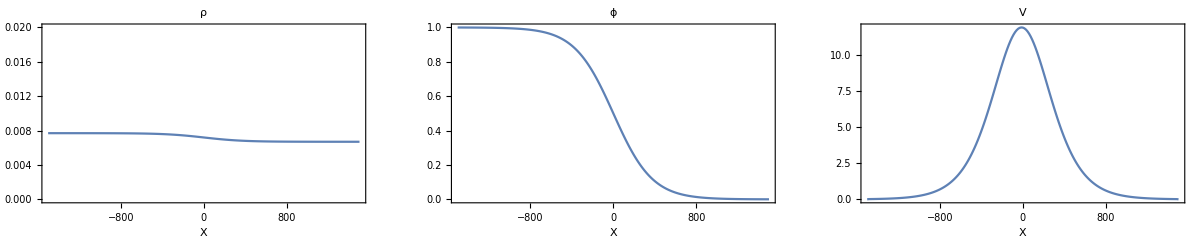

```mathematica
(* Plot as graphics row *)
tplot= 1; (*Index of time point to plot*)
plotOptions = {ImageSize-> Medium,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->10,GrayLevel[0]}, Frame-> True, FrameLabel->{"X", None}};
p1=ListPlot[  Transpose[{xmesh, ρAll[[;;, tplot]]}], Joined-> True ,PlotRange-> {Automatic, {0, 0.02}}, PlotLabel->"ρ", plotOptions];
p2=ListPlot[  Transpose[{xmesh, ϕAll[[;;, tplot]]}], Joined-> True, PlotRange-> {Automatic, {0, 1}}, PlotLabel->"ϕ",plotOptions];
p3=ListPlot[  Transpose[{xmesh, VAll[[;;, tplot]]}], Joined-> True, PlotLabel->"V",plotOptions];
Print["Timepoint ", tplot, "/", T]
GraphicsRow[{p1,p2,p3}, ImageSize->Full]
(*Show[p1,p2,p3, PlotRange-> All]*)
```

### Plot together with experimental data

#### Plot average interface position

We now estimate the displacement of the wave profile over time in two ways: 
1. According to the position where ϕ(x)=1/2, which initially is at x=0.
2. According to the peak of V(x). This is only relevant for the parameters for which the solution of V(X) shows a single peak at x=0 at t=0.

According to position of ϕ=1/2

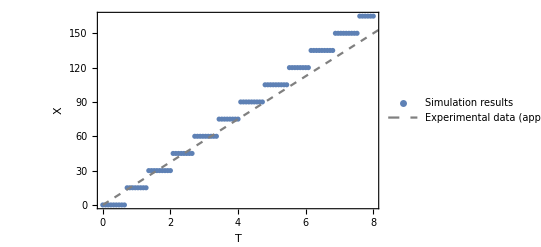

```mathematica
indices=Flatten@Map[ FirstPosition[#, True]&, Transpose@Map[  (#<0.5)&, ϕAll, {2}  ]];
positions = Map[ xmesh[[#]]&, indices]-xmesh[[indices[[1]]]];

p1=ListPlot[ Transpose[{tmesh, positions}], PlotLegends-> {"Simulation results"} ];
p2=ListPlot[{{tmesh[[-1]], positions[[-1]]}, {tmesh[[1]],  positions[[1]]}}, Joined-> True, PlotStyle->Dashed, PlotLegends-> {"Fit through first and last data points"}];
p3=Plot[75/4 x,{x,0,T}, PlotStyle->{Dashed, Gray}, PlotLegends-> {"Experimental data (approx.)"}];
Show[p1,p3, Frame-> True, FrameLabel->{"T", "X"}]
```

According to position of V (peak)

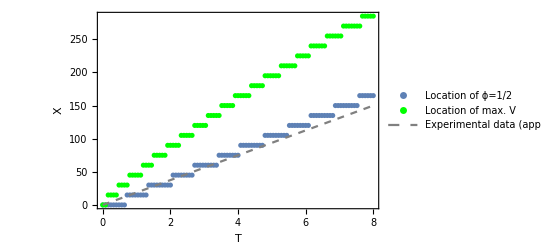

```mathematica
indices2=Flatten@Table[ Position[ VAll[[;;,ti]], Max@VAll[[;;,ti]] ], {ti, 1, T+1}];
positions2 = Map[ xmesh[[#]]&, indices2]-xmesh[[indices2[[1]]]];

p1=ListPlot[ Transpose[{tmesh, positions}], PlotLegends-> {"Location of ϕ=1/2"}, PlotStyle->{Default}];
p2=ListPlot[ Transpose[{tmesh, positions2}], PlotLegends-> {"Location of max. V"}, PlotStyle->{Green}];
p3=Plot[75/4 x,{x,0,tmax}, PlotStyle->{Dashed, Gray}, PlotLegends-> {"Experimental data (approx.)"}];
Show[p1,p2,p3, PlotRange-> Full, Frame-> True, FrameLabel->{"T", "X"}]
```

#### Plot V(x) with experimental data

Now we plot the solution for V(x) together with some experimental data.

```mathematica
(* Load experimental data *)
dataPath=FileNameJoin[{NotebookDirectory[], "Data", "Velocities_means.csv"}];
data=Import[dataPath, "CSV"];
(* headers=First[data]; (*original headers*) *)
headers={"Location", "X","V","eX","eV"};
rows=Rest[data];
dataset=Dataset[AssociationThread[headers,#]&/@rows];
dataset
```

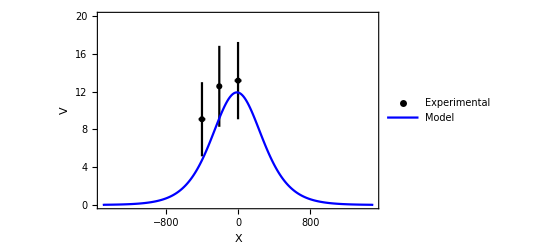

```mathematica
Needs["ErrorBarPlots`"]

(*Extract data from the DataSet*)
dataList=Normal[dataset];

(*Extract x,y,ex,and ey from the data list*)
plotData=dataList[[All,headers[[2;;]]]];
formattedData={{#X,#V},ErrorBar[#eX,#eV]}&/@plotData;

(*Create the error bar plot*)
ebPlot =ErrorListPlot[formattedData,PlotTheme->"Detailed",AxesLabel->{"x","y"},PlotMarkers->Automatic,GridLines->None, PlotRange->{{-L, L}, {0, 20}}, PlotStyle-> {Black}, PlotLegends-> {"Experimental"}];
vPlot=ListPlot[  Transpose[{xmesh, VAll[[;;, tplot]]}], Joined-> True, PlotLabel->"V",PlotStyle-> {Blue}, PlotLegends-> {"Model"}];
Show[ebPlot, vPlot, FrameLabel-> {"X", "V"}]
```

### Save results

Save simulation results as separate CSV files for the list of parameters, ρ, ϕ and V.

```mathematica
(*Save path and filename pattern*)
filenamePattern=DateString[{"ISODate","_", "Hour", "Minute"}]; (* use current date and time*)
OutNameRoot =FileNameJoin[{NotebookDirectory[], "Model_results", filenamePattern}]
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/For_publication/Model_results/2024-07-20_1242

```mathematica
allParams={eO,eM,η,γ,τ,D1,α,ρdA,ρdB,ρh,aρ,aϕ,"L","tmax","Nx","T"} ;
allValues=allParams /. params /. {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T};
allParamsOut =Transpose[{allParams, allValues}];
```

```mathematica
(* Export parameters*)
(*AllParams=Join[ params, {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T, "Dirichlet Boundaries"}]*)
allParams={eO,eM,η,γ,τ,D1,α,ρdA,ρdB,ρh,aρ,aϕ,"L","tmax","Nx","T"} ;
allValues=allParams /. params /. {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T};
allParamsOut =Transpose[{allParams, allValues}];
Export[StringJoin[OutNameRoot, "_data_parameters.csv"], allParamsOut, "csv"]
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/For_publication/Model_results/2024-07-20_1242_data_parameters.csv

```mathematica
(*dataSave =Map[DecimalForm[#, dec]&, N[ρAll, dec], {2}];*)
Clear[dataSave];dataSave = N[ρAll]// TableForm;
Export[StringJoin[OutNameRoot, "_data_rho_1.csv"], dataSave, "CSV"]
Clear[dataSave];dataSave = N[ϕAll]// TableForm;
Export[StringJoin[OutNameRoot, "_data_phi_1.csv"], dataSave, "CSV"]
Clear[dataSave];dataSave =N[VAll] // TableForm;
Export[StringJoin[OutNameRoot, "_data_V_1.csv"], dataSave, "CSV"]
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/For_publication/Model_results/2024-07-20_1242_data_rho_1.csv

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/For_publication/Model_results/2024-07-20_1242_data_phi_1.csv

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/For_publication/Model_results/2024-07-20_1242_data_V_1.csv

### Compute single-cell trajectories

Here, we compute the velocity of a single cell starting at a location x using the velocity profile V(x, t) through
	x(t+1) = x(t) + v(x(t), t)*Δt.

First, we define an interpolation function for the velocity profile V(x,t) based on the discrete solution and plot the result.

InterpolatingFunction[…]

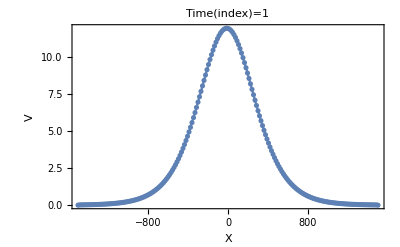

```mathematica
ti=1;
dataTmp =Transpose[{xmesh, VAll[[;;, ti]]}];
InterpolationV =Interpolation[ dataTmp, InterpolationOrder->1]
p1=ListPlot[dataTmp ];
p2=Plot[InterpolationV[x], {x, -L , L}];
Show[p1, p2, PlotRange-> All, Frame-> True, FrameLabel-> {"X", "V"}, PlotLabel-> StringJoin["Time(index)=",ToString[ti]]]
```

Now we compute the location of a cell starting at one of the selected initial positions. 
Initial positions to take: 0, -200, -400 μm, corresponding to the locations of the tracked cells in the experiments.

```mathematica
(* use same filenamePattern as above*)
RootFolder = FileNameJoin[{NotebookDirectory[], "Model_results", StringJoin[filenamePattern, "_1cell"]}];

(*Settings*)
IntOrder=1; (*interpolation order*)
xCell0List = {0, -200, -400};
(*sim=1;*)

xCellAllAll = {};
vCellAllAll = {};

For[sim=1, sim<= Length[xCell0List],sim++,
Print[sim];

(* interpolation func*)
xCell0 = xCell0List[[sim]]; (*initial position of tracked cell*)
tIdx =1;
dataTmp =Transpose[{xmesh, VAll[[;;, tIdx]]}];
InterpolationV0 =Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCell0=InterpolationV0[xCell0];
xCellAll={xCell0};
vCellAll={vCell0};
For[tIdx=2, tIdx≤ T+1, tIdx++,
xCellTmp = xCellAll[[-1]];
vCellTmp=vCellAll[[-1]];
xCellNew =xCellTmp+vCellTmp*ΔtSet;

(* define new interpolation func*)
dataTmp =Transpose[{xmesh, VAll[[;;, tIdx]]}];
InterpolationVTmp =Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCellNew = InterpolationVTmp[xCellNew];

(* add results to lists *)
AppendTo[xCellAll, xCellNew];
AppendTo[vCellAll, vCellNew];
];

(* Save results *)
AppendTo[xCellAllAll, xCellAll];
AppendTo[vCellAllAll, vCellAll];

settingsToSave={{"xCell0", xCell0},{"IntOrder", IntOrder}};
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_xCellAll.csv"]}], xCellAll, "CSV"];
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_vCellAll.csv"]}], vCellAll, "CSV"];
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_settings.csv"]}], settingsToSave, "CSV"];

]
```

1

2

3

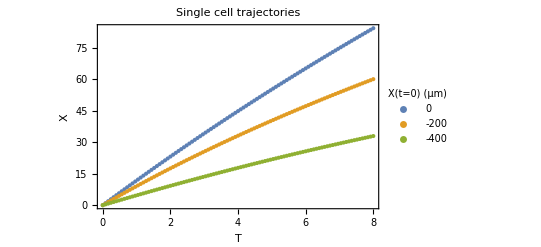

```mathematica
ListPlot[ Table[ Transpose[{tmesh, xCellAllAll[[i,;;]]-xCell0List[[i]]  }], {i, 1, 3}  ],PlotLegends->Placed[LineLegend[ToString/@xCell0List,LegendLabel->"X(t=0) (μm)"],Right], Frame-> True, FrameLabel-> {"T", "X"}, PlotLabel-> "Single cell trajectories"]
```

## Calculate the front velocity

This section computes the velocity of the wave front by translating the wave front at a given time to match that at another time and identifying the optimal translation distance in order to compute an estimation of the velocity.

### Calculate Δϕ

Numerically solve for wave velocity by shifting the profile ϕ[x, t] to ϕ[x + v δt, t + δt] and finding v for which the difference | ϕ[x, t] - ϕ[x + v δt, t + δt] | is minimized. 
Do for a range of values of t (denoted t1), but only one δt should be sufficient.
Boundaries: -L <= xp+vp δt <= L, so xp <= L - vp δt, so need to set this as integral / sum upper bound

```mathematica
(*Numerically test across a range of values for t and v*)
T1=20;δt=30;
t1All = Range[T1, T-δt, δt]; (* set time range*)
t1len= Length@t1All;
vpList=Range[0, 0.5*δt]/δt;
```

```mathematica
(*Test *)
(*(ϕAll[[x, t]]-ϕAll[[x+vp dt, t+dt]] )/.{x-> Nx/2, t-> T/2, vp-> vpList[[1]],dt -> 10}*)
```

Note: smallest possible difference in v testable is ΔxSet/δt, as the mesh size ΔxSet is fixed.
Testable difference in V (μm/hr):

```mathematica
N[ΔxSet/δt]
```

0.5

```mathematica
Module[{dt = δt},
ΔϕFull=Abs[
Table[
Sum[ (ϕAll[[x, t1All[[tj]] ]]-ϕAll[[x+vpList[[vj]] dt, t1All[[tj]]+dt]] ), {x, 1, Nx-vpList[[vj]] dt}],
{tj, 1, t1len}, {vj, 1, Length[vpList]}
]
];
]
(*ΔϕFull=Table[  NIntegrate[Abs[((ϕsol/.{t->t1, x->xp})-(ϕsol/.{t->t1+δt, x->xp+vp δt} ) )] /.{x->xp} , {xp, -L, L-vp δt}, MaxRecursion->12],  {t1, t1All[[1]], t1All[[-1]], δt }, {vp, vpList[[1]], vpList[[-1]], δvp}];*)
```

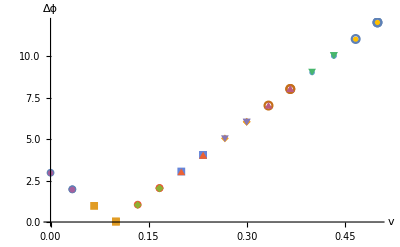

```mathematica
t1temp=ConstantArray[vpList, t1len] ;
plotdata=Partition[  Transpose[ {Flatten@t1temp, Flatten@ΔϕFull} ] , t1len];hplot=ListPlot[plotdata, Frame->False, PlotMarkers->{Automatic, 8},AxesLabel->{Style["v",Black, FontSize-> 20],Style["Δϕ", Black,FontSize-> 20] }, TicksStyle->Directive[Black,16]]
```

In the plot above, the location of the minimal Δϕ corresponds to the optimal shift. The value of v (in units of the mesh) is the optimal velocity.

#### Find optimal v

```mathematica
(*Find minima of Δϕ for each t1*)
findmin=Position[#,Min[#]]&;
ϕminPos=Flatten[findmin/@ΔϕFull];
vValsϕmin = vpList[[ ϕminPos ]] (*values of velocity where the difference is minimal *)
```

{1/10,1/10}

```mathematica
(*Find minimal distance averaged over all t1*)
Δϕavg=Mean[ΔϕFull];
vInferred =vpList[[ Sequence@@First@findmin[Δϕavg] ]]  (* "optimal v" *)
```

1/10

```mathematica
ΔϕInferred= Δϕavg[[ Sequence@@First@findmin[Δϕavg] ]]
```

0.0372829

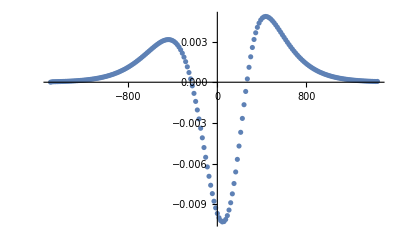

```mathematica
(* Plot difference between profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
δvals=Table[ϕAll[[x, t1 ]]-ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]
p1=ListPlot[Transpose[{xvals, δvals}],PlotRange-> All,PlotLegends->"Δϕ"]
```

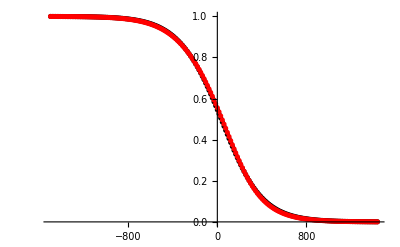

```mathematica
(* Plot the shifted and the unshifted profiles together *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
ϕ1vals=Table[ϕAll[[x, t1 ]], {x, 1, Nx-vInferred dt}];
ϕ2vals=Table[ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]
p1=ListPlot[Transpose[{xvals, ϕ1vals}],PlotRange-> All,PlotLegends->"ϕ1", PlotStyle-> {Black}];
p2=ListPlot[Transpose[{xvals, ϕ2vals}],PlotRange-> All,PlotLegends->"ϕ2", PlotStyle-> {Red}];
Show[p1,p2]
```

Estimated wave velocity in units of μm/hr:

```mathematica
N[vInferred*ΔxSet/ΔtSet]
```

18.75

### Organize data together and save

Save parameters + inferred v + error Δϕ

```mathematica
params
```

{ρdA→0.0067,ρdB→0.0077,D1→15,eO→12960,eM→1944/5,τ→10,η→18/5,γ→2.88,α→3.5×10^-6,ρh→1/1000,aρ→4,aϕ→4}

```mathematica
(*vars={{τ,ρdA,ρdB,ρh},{D1,α,kF},{fc,ξ,χ,η,κ},{sM,sO,a,τs}};*)
vars = {eO,eM,η,γ,τ,D1,α,ρdA,ρdB,aρ,aϕ,ρh};
varsVals=Map[Replace[#, Flatten@params]&,vars, 2]
```

{12960,1944/5,18/5,2.88,10,15,3.5×10^-6,0.0067,0.0077,4,4,1/1000}

deltavUnits:

```mathematica
varsOut=ToString/@{{eO,eM,eta,xi,tau,D1,alpha,rhodA,rhodB,aRho,aPhi,rhoh},{"xmin", "xmax", "tmax", "deltat", "deltavUnits"},{"vInferred", "DeltaphiInferred", "vInferredMicrons", "phiWidthMicrons"}}
varsValsOut=N/@Join[varsVals,{{-L,L,tmax,δt,ΔxSet/δt}},{{vInferred, ΔϕInferred, vInferred*ΔxSet/ΔtSet, ϕwidth}}]
```

{{eO, eM, eta, xi, tau, D1, alpha, rhodA, rhodB, aRho, aPhi, rhoh},{xmin, xmax, tmax, deltat, deltavUnits},{vInferred, DeltaphiInferred, vInferredMicrons, phiWidthMicrons}}

{12960.,388.8,3.6,2.88,10.,15.,3.5×10^-6,0.0067,0.0077,4.,4.,0.001,{-1500.,1500.,8.,30.,0.5},{0.1,0.0372829,18.75,ϕwidth}}

```mathematica
fnameOut=StringJoin[NotebookDirectory[],"Model_results/", filenamePattern,  "_wave_velocity_est.csv"];
Export[fnameOut, {varsOut,varsValsOut}, "CSV"]
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/For_publication/Model_results/2024-07-20_1242_wave_velocity_est.csv

## Load saved results

Warning: some of the loaded numbers (stored as fractions) are imported as strings rather than numbers and might require manual correction.

```mathematica
filenamePattern = "best_model";
InNameRoot =FileNameJoin[{NotebookDirectory[], "Model_results", filenamePattern}]
ρAll=Import[ StringJoin[InNameRoot, "_data_rho_1.csv"] ];
ϕAll=Import[ StringJoin[InNameRoot, "_data_phi_1.csv"] ];
VAll=Import[ StringJoin[InNameRoot, "_data_V_1.csv"] ];
```

/Users/ydang3/Documents/Projects_Dresden/Tabler_SkullWave/SkullWave/For_publication/Model_results/best_model

```mathematica
parameters=Import[ StringJoin[InNameRoot, "_data_parameters.csv"] ]
params=Thread[ToExpression@parameters[[;;, 1]]-> parameters[[ ;;, 2]] ]

Clear[Nx, tmax, T, L];
Nx=parameters[[ FirstPosition[ Map[#=="Nx"&, parameters[[;;, 1]]], True], 2 ]][[1]];
tmax=parameters[[ FirstPosition[ Map[#=="tmax"&, parameters[[;;, 1]]], True], 2 ]][[1]];
T=parameters[[ FirstPosition[ Map[#=="T"&, parameters[[;;, 1]]], True], 2 ]][[1]];
L=parameters[[ FirstPosition[ Map[#=="L"&, parameters[[;;, 1]]], True], 2 ]][[1]];

ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;

xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
```

{{eO,12960},{eM,1944/5},{η,18/5},{γ,2.88},{τ,10},{D1,15},{α,3.5×10^-6},{ρdA,0.0067},{ρdB,0.0077},{ρh,1/1000},{aρ,4},{aϕ,4},{L,1500},{tmax,8},{Nx,200},{T,100}}

{eO→12960,eM→1944/5,η→18/5,γ→2.88,τ→10,D1→15,α→3.5×10^-6,ρdA→0.0067,ρdB→0.0077,ρh→1/1000,aρ→4,aϕ→4,1500→1500,8→8,200→200,100→100}